```mathematica
prompt = Sort[{{11,304},{0,73},{2,218},{16,310},{24,40},{18,329},{20,263},{19,304},{13,302},{12,321},{10,347},{4,346},{3,294},{6,324}}]
```

(0 | 73
2 | 218
3 | 294
4 | 346
6 | 324
10 | 347
11 | 304
12 | 321
13 | 302
16 | 310
18 | 329
19 | 304
20 | 263
24 | 40)

```mathematica
FindFit[prompt,A*1/(σ*Sqrt[2 π]) Exp[-(1/2) ((x-μ)/σ)^2],{σ,μ,A},x]
```

{σ→9.27121,μ→11.1324,A→8259.75}

```mathematica
{σ->9.271206208920976,μ->11.1323578147517,A->8259.747942414977}
```

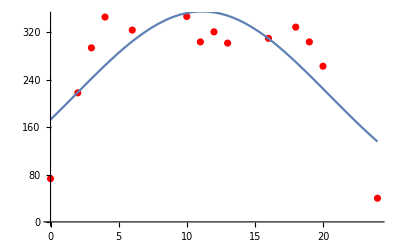

```mathematica
Show[ListPlot[prompt,PlotStyle->Red],Plot[(A Exp[-1/2 ((x-μ)/σ)^2])/(σ √(2 π))/.{σ->9.271206208920976,μ->11.1323578147517,A->8259.747942414977},{x,0,24}]]
```

```mathematica
fwhm = 2Sqrt[2*Log[2]]*9.27121
```

21.832

```mathematica
NonlinearModelFit[prompt,A*1/(σ*Sqrt[2 π]) Exp[-(1/2) ((x-μ)/σ)^2],{σ,μ,A},x]
```

FittedModel[355.419 ⅇ^(-0.00581698 (x-«17»)^2)]